## Projected trap analysis

## image processing

```mathematica
imagedir="trap_array_images\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],imagedir}]];
```

```mathematica
(*imagedir="../trap_array_images/";
SetDirectory[imagedir+NotebookDirectory[]];*)
img = ColorConvert[Import["array_more_closed_20200825.jpg"],"grayscale"]
```

-Graphics-

```mathematica
Show[ImageRotate[img,-0.01], ImageSize-> Medium]
```

-Graphics-

```mathematica
data = ImageData[ImageRotate[img,-0.01]];
data = data-data[[50,50]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data]; 
lenx = data//Length;
leny= data[[1]]//Length;
```

```mathematica
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{860,1},{880,lenx}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[860;;861, 1;; leny]]]
```

-Graphics-

```mathematica
Image[data[[869;;870,1;;leny]]]
```

-Graphics-

0.0627451

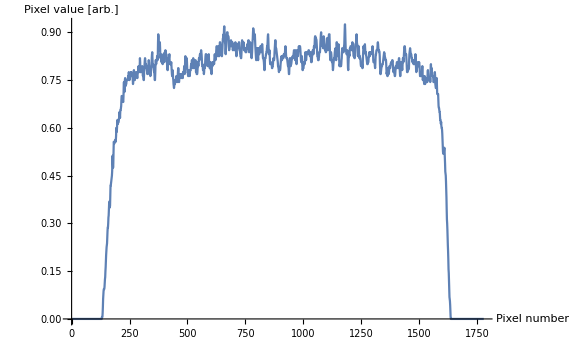

```mathematica
linedata = Transpose@{Range[leny],data[[860;;861,1;;leny]][[1]]};
ListPlot[linedata, Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large]
```

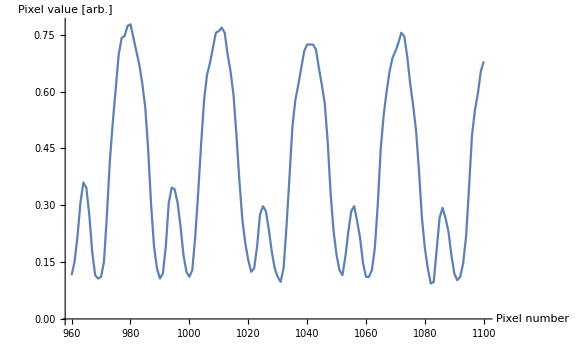

```mathematica
ListPlot[linedata[[960;;1100]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

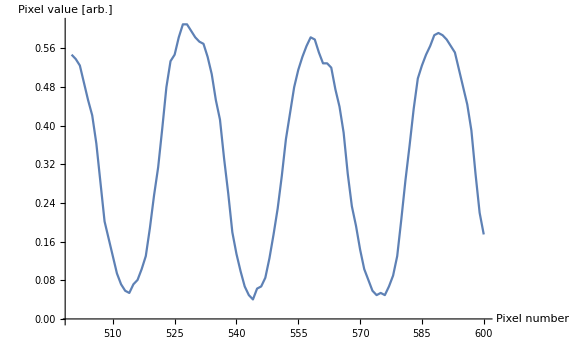

```mathematica
ListPlot[linedata[[500;;600]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

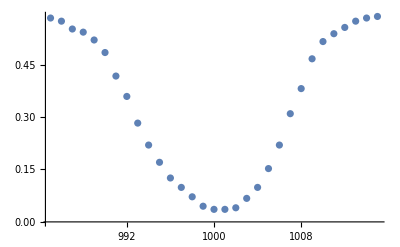

```mathematica
ListPlot[linedata[[985;;1015]]]
```

```mathematica
model = A (1-   Exp[(-2(x-μ)^2)/σ^2]);
fit =FindFit[linedata[[979;;1021]],model,{{μ,1000},σ,A, {b,0.5}},x]
Show[Plot[model/.fit,{x,985,1015}],ListPlot[linedata[[985;;1015]]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Medium]
pixel = 1.12; (*μm*)
StringForm["real space waist `` [μm]",Values[fit[[2]]]*pixel]
```

{μ→999.981,σ→10.6518,A→0.561076,b→0.5}

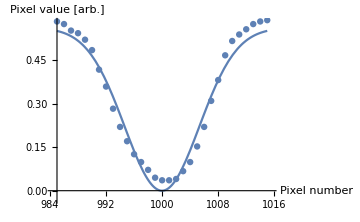

real space waist 11.93 [μm]

```mathematica
Values[fit[[2]]]
```

6.01289

real space waist 1.12 (σ→6.01289) [μm]

```mathematica
sigma = 8.335; pixsize = 4/1750//N
```

0.00228571

1.7 um per pixel,

```mathematica
8*2.3
```

18.4

```mathematica
14 um
```

```mathematica
0.56/ⅇ^2//N
```

0.0757878

## atomic trap depth

For a dark spot array, let P be the total power incident on the array mask. 
Mark says It = Id, so It = P_unit/d^2;

```mathematica
d = .430;(*array period, input plane*)
a = .100; (*array spot radius*)
A =14.8^2(* π 12^2*); (*the area of a 25.4mm disk optic*)
M = 1/100;(*array magnification*)
It=P/A;
```

```mathematica
It*10^-6(1/M)^2/.P-> 1.5(*site peak intensity in W/μm^2*)
```

0.0000684806

```mathematica
kB = 1.38*^-23;
c=2.998*^8;
ϵ0 = 8.85*^-12;
λ = 8.52*^-7;
ω0 = 2π c/λ;
ℏ= 1.05*10^-34;
Γ = 2π 5.2227*10^6; (*Cesium D2 line*)
Δ= 2π(c/(8.05*^-7)-c/λ);
Udip = (3 π c^2 Γ)/(2 ω0^3 Δ);(*dipole trap potential seen by atom in units intensity*)
```

```mathematica
T/(2/(3 kB)Udip)10^-12/.T-> .0005(*intensity in W/m^2 reqd for desired trap depth*)
```

0.00103884

```mathematica
2/(3kB)Udip*It/.P->1.5
```

3.296×10^-15

Trent: 121 ~2x2 um sites, 500 mW--> site intensity is ~ 1mW/um

```mathematica
.5/(121)
```

```mathematica
0.004132231404958678
```

```mathematica
Clear[P]
```

```mathematica
Solve[P/(A 10^6)(1/M)^2==1,P]
```

{{P→21904.}}

```mathematica
A*10^6 M^2.001(*required power in W*)
```

21.904

```mathematica
500
```